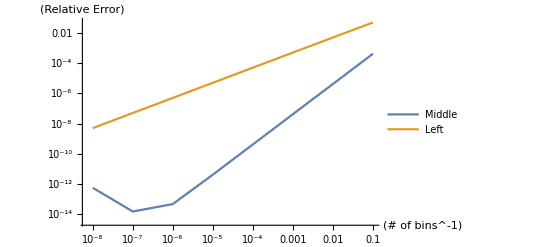

```mathematica
exact = Integrate[Exp[x],{x,0,1}];
SetDirectory["/home/ethan/spring20/comphys/week2/rooney/"];
getres[n_,i_]:=ReadList["!./integrate "<>ToString[n]<>" | awk '{print $"<>ToString[i]<>"}'",Number][[1]];
resleft=Table[{1/n,Abs[(getres[n,1]-exact)/exact]},{n,{10,100,1000,10000,100000,1000000,10000000, 100000000}}];
resmiddle=Table[{1/n,Abs[(getres[n,2]-exact)/exact]},{n,{10,100,1000,10000,100000,1000000,10000000, 100000000}}];
ListLogLogPlot[{resleft,resmiddle}, Joined->True, PlotLegends->{"Middle", "Left"}, AxesLabel->{"(# of bins^-1)","(Relative Error)"}]
```

exactpen

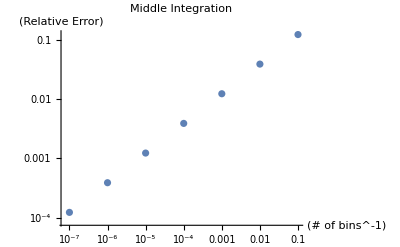

```mathematica
getrespen15[n_]:=ReadList["!./p415 "<>ToString[n],Number][[1]];
thetanot = Pi/6;
exactpen15 = Integrate[1/Sqrt[2*9.81(Cos[theta]-Cos[thetanot])],{theta, -thetanot, thetanot}];
Print[exactpen];
resleftpen15=Table[{1/n,Abs[(getrespen15[n]-exactpen15)/exactpen15]},{n,{10,100,1000,10000,100000,1000000,10000000}}];
ListLogLogPlot[resleftpen15, Joined->False, AxesLabel->{"(# of bins^-1)","(Relative Error)"}, PlotLabel->"Middle Integration"]
```

exactpen

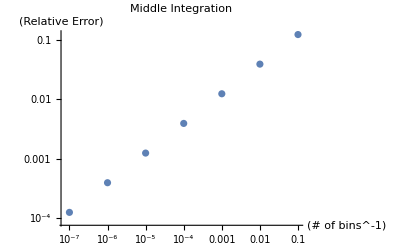

```mathematica
getrespen30[n_]:=ReadList["!./p430 "<>ToString[n],Number][[1]];
thetanot = Pi/3;
exactpen30 = Integrate[1/Sqrt[2*9.81(Cos[theta]-Cos[thetanot])],{theta, -thetanot, thetanot}];
Print[exactpen];
resleftpen30=Table[{1/n,Abs[(getrespen30[n]-exactpen30)/exactpen30]},{n,{10,100,1000,10000,100000,1000000,10000000}}];
ListLogLogPlot[resleftpen30, Joined->False, AxesLabel->{"(# of bins^-1)","(Relative Error)"}, PlotLabel->"Middle Integration"]
```

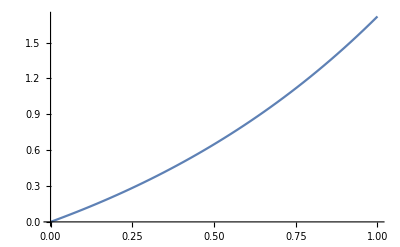

ReadList::readn: Invalid real number found when reading from !/home/ethan/spring20/comphys/week2/rooney/p1 -l 4.

{{0.,0.},{0.25,0.283287},{0.5,0.647035},{0.75,1.1141},$Failed}

ReadList::readn: Invalid real number found when reading from !/home/ethan/spring20/comphys/week2/rooney/p1 -l 10.

{{0.,0.},{0.1,0.105127},{0.2,0.221311},{0.3,0.349713},{0.4,0.49162},{0.5,0.648451},{0.6,0.821776},{0.7,1.01333},{0.8,1.22503},{0.9,1.459},$Failed}

ReadList::readn: Invalid real number found when reading from !/home/ethan/spring20/comphys/week2/rooney/p1 -l 50.

{{0.,0.},{0.02,0.020201},{0.04,0.0408101},{0.06,0.0618355},{0.08,0.0832857},{0.1,0.105169},{0.12,0.127495},{0.14,0.150271},{0.16,0.173508},{0.18,0.197214},{0.2,0.221399},{0.22,0.246073},{0.24,0.271245},{0.26,0.296925},{0.28,0.323124},{0.3,0.349853},{0.32,0.377121},{0.34,0.404941},{0.36,0.433322},{0.38,0.462277},{0.4,0.491817},{0.42,0.521953},{0.44,0.552698},{0.46,0.584064},{0.48,0.616064},{0.5,0.64871},{0.52,0.682016},{0.54,0.715995},{0.56,0.75066},{0.58,0.786025},{0.6,0.822105},{0.62,0.858914},{0.64,0.896466},{0.66,0.934777},{0.68,0.973862},{0.7,1.01374},{0.72,1.05442},{0.74,1.09592},{0.76,1.13826},{0.78,1.18145},{0.8,1.22552},{0.82,1.27048},{0.84,1.31635},{0.86,1.36314},{0.88,1.41088},{0.9,1.45958},{0.92,1.50927},{0.94,1.55996},{0.96,1.61167},{0.98,1.66443},$Failed}

ReadList::readn: Invalid real number found when reading from !/home/ethan/spring20/comphys/week2/rooney/p1 -m 4.

{{0.,0.},{0.25,0.25},{0.5,0.571006},{0.75,0.983187},$Failed}

ReadList::readn: Invalid real number found when reading from !/home/ethan/spring20/comphys/week2/rooney/p1 -m 10.

{{0.,0.},{0.1,0.1},{0.2,0.210517},{0.3,0.332657},{0.4,0.467643},{0.5,0.616826},{0.6,0.781698},{0.7,0.96391},{0.8,1.16529},{0.9,1.38784},$Failed}

ReadList::readn: Invalid real number found when reading from !/home/ethan/spring20/comphys/week2/rooney/p1 -m 50.

{{0.,0.},{0.02,0.02},{0.04,0.040404},{0.06,0.0612202},{0.08,0.082457},{0.1,0.104123},{0.12,0.126226},{0.14,0.148776},{0.16,0.171782},{0.18,0.195252},{0.2,0.219196},{0.22,0.243624},{0.24,0.268546},{0.26,0.293971},{0.28,0.319909},{0.3,0.346372},{0.32,0.373369},{0.34,0.400912},{0.36,0.429011},{0.38,0.457677},{0.4,0.486923},{0.42,0.516759},{0.44,0.547199},{0.46,0.578253},{0.48,0.609934},{0.5,0.642256},{0.52,0.67523},{0.54,0.708871},{0.56,0.743191},{0.58,0.778204},{0.6,0.813925},{0.62,0.850367},{0.64,0.887546},{0.66,0.925476},{0.68,0.964171},{0.7,1.00365},{0.72,1.04392},{0.74,1.08501},{0.76,1.12693},{0.78,1.1697},{0.8,1.21333},{0.82,1.25784},{0.84,1.30325},{0.86,1.34958},{0.88,1.39684},{0.9,1.44506},{0.92,1.49425},{0.94,1.54443},{0.96,1.59563},{0.98,1.64787},$Failed}

{{0.,0.},{0.25,0.283287},{0.5,0.647035},{0.75,1.1141},$Failed}

```mathematica
exactplot = Plot[Exp[x]-1,{x,0,1}, PlotLegends-> "f(x)"]
middle4 =ReadList["!/home/ethan/spring20/comphys/week2/rooney/p1 -l 4", {Number, Number}]
middle10 =ReadList["!/home/ethan/spring20/comphys/week2/rooney/p1 -l 10", {Number, Number}]
middle50= ReadList["!/home/ethan/spring20/comphys/week2/rooney/p1 -l 50", {Number, Number}]
left4 = ReadList["!/home/ethan/spring20/comphys/week2/rooney/p1 -m 4", {Number, Number}]
left10 = ReadList["!/home/ethan/spring20/comphys/week2/rooney/p1 -m 10", {Number, Number}]
left50 = ReadList["!/home/ethan/spring20/comphys/week2/rooney/p1 -m 50", {Number, Number}]
Print[middle4]
```

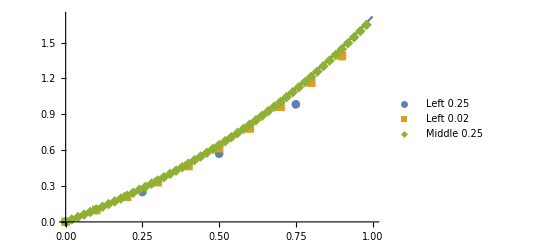

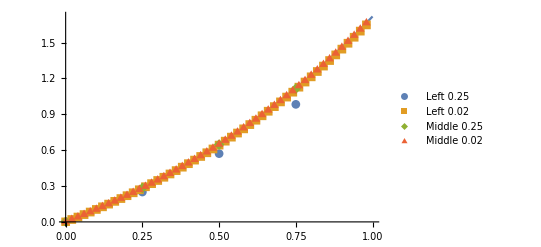

```mathematica
points = ListPlot[{ left4,left10, left50},PlotMarkers->Automatic, PlotLegends-> PointLegend[{"Left 0.25", "Left 0.02", "Middle 0.25", "Middle 0.02"}, LegendFunction->Frame]];
Show[{exactplot, points}]
```